## Te=3 keV Ti= 3keV ne=10^25cm^-3 α projectile: 001

### plotting dE/dx vs E from dedx.out file

```mathematica
st=OpenRead["dedx.001.out"];
Do[Read[st,String],{i,1,19}];
ne=Read[st,Number]
Te=Read[st,Number]
Ti=Read[st,Number]
nn=Read[st,Number]
proj=Read[st,{Number,Number,Number}]
nts=nn+1; (* stop reading when Ep goes critical,
            in this case when Ep < 0 *)
data=
Table[Read[st,{Number,Number,Number,Number,Number}],{i,1,nts}];
Close[st];
data
```

1.×10^25

3.

3.

300

{3540.,3.75309×10^6,2.}

{{0,0.00001,-323.936,-320.103,-3.8326},{1,11.8,0.251461,0.245125,0.00633603},{2,23.6,0.212202,0.200093,0.0121092},{3,35.4,0.168949,0.152993,0.0159556},{4,47.2,0.141709,0.1227,0.0190091},{5,59.,0.124071,0.102448,0.0216224},{6,70.8,0.112035,0.0880895,0.0239459},{7,82.6,0.10345,0.07739,0.0260595},{8,94.4,0.0971145,0.0691029,0.0280116},{9,106.2,0.0923224,0.0624883,0.0298341},{10,118.,0.0886306,0.057081,0.0315497},{11,129.8,0.0857469,0.0525718,0.0331751},{12,141.6,0.0834783,0.0487552,0.0347231},{13,153.4,0.0816827,0.0454791,0.0362036},{14,165.2,0.0802592,0.0426346,0.0376245},{15,177.,0.0791329,0.0401404,0.0389925},{16,188.8,0.0782452,0.0379323,0.0403129},{17,200.6,0.0775573,0.035967,0.0415903},{18,212.4,0.0770325,0.0342039,0.0428286},{19,224.2,0.076644,0.0326131,0.044031},{20,236.,0.0763703,0.0311699,0.0452004},{21,247.8,0.0761937,0.0298544,0.0463393},{22,259.6,0.0761001,0.0286501,0.04745},{23,271.4,0.0760775,0.0275433,0.0485343},{24,283.2,0.0761163,0.0265223,0.049594},{25,295.,0.0762081,0.0255774,0.0506306},{26,306.8,0.0763459,0.0247003,0.0516456},{27,318.6,0.076524,0.0238838,0.0526401},{28,330.4,0.0767372,0.0231217,0.0536154},{29,342.2,0.0769812,0.0224087,0.0545724},{30,354.,0.0772523,0.0217401,0.0555122},{31,365.8,0.0775473,0.0211119,0.0564355},{32,377.6,0.0778634,0.0205203,0.0573431},{33,389.4,0.0781981,0.0199623,0.0582359},{34,401.2,0.0785493,0.0194349,0.0591144},{35,413.,0.0789151,0.0189358,0.0599793},{36,424.8,0.0792939,0.0184627,0.0608312},{37,436.6,0.0796841,0.0180135,0.0616706},{38,448.4,0.0800845,0.0175864,0.062498},{39,460.2,0.0804939,0.0171799,0.0633139},{40,472.,0.0809113,0.0167925,0.0641188},{41,483.8,0.0813357,0.0164228,0.064913},{42,495.6,0.0817665,0.0160696,0.0656969},{43,507.4,0.0822027,0.0157318,0.0664709},{44,519.2,0.0826438,0.0154084,0.0672354},{45,531.,0.0830892,0.0150986,0.0679906},{46,542.8,0.0835383,0.0148014,0.0687369},{47,554.6,0.0839906,0.014516,0.0694745},{48,566.4,0.0844457,0.0142419,0.0702038},{49,578.2,0.0849032,0.0139783,0.0709249},{50,590.,0.0853628,0.0137246,0.0716382},{51,601.8,0.0858241,0.0134802,0.0723439},{52,613.6,0.0862869,0.0132447,0.0730422},{53,625.4,0.0867508,0.0130176,0.0737332},{54,637.2,0.0872156,0.0127984,0.0744173},{55,649.,0.0876812,0.0125866,0.0750945},{56,660.8,0.0881472,0.0123821,0.0757651},{57,672.6,0.0886135,0.0121842,0.0764293},{58,684.4,0.08908,0.0119929,0.0770872},{59,696.2,0.0895465,0.0118076,0.077739},{60,708.,0.0900129,0.0116281,0.0783848},{61,719.8,0.090479,0.0114542,0.0790247},{62,731.6,0.0909447,0.0112856,0.079659},{63,743.4,0.0914099,0.0111221,0.0802878},{64,755.2,0.0918745,0.0109633,0.0809111},{65,767.,0.0923384,0.0108092,0.0815292},{66,778.8,0.0928016,0.0106595,0.0821421},{67,790.6,0.0932639,0.010514,0.0827499},{68,802.4,0.0937253,0.0103725,0.0833528},{69,814.2,0.0941858,0.010235,0.0839508},{70,826.,0.0946452,0.0101011,0.0845441},{71,837.8,0.0951036,0.0099708,0.0851328},{72,849.6,0.0955609,0.00984393,0.085717},{73,861.4,0.096017,0.00972034,0.0862967},{74,873.2,0.0964719,0.00959991,0.086872},{75,885.,0.0969256,0.00948252,0.0874431},{76,896.8,0.097378,0.00936805,0.08801},{77,908.6,0.0978291,0.0092564,0.0885727},{78,920.4,0.098279,0.00914746,0.0891315},{79,932.2,0.0987274,0.00904112,0.0896863},{80,944.,0.0991745,0.00893731,0.0902372},{81,955.8,0.0996203,0.00883592,0.0907844},{82,967.6,0.100065,0.00873688,0.0913277},{83,979.4,0.100508,0.0086401,0.0918675},{84,991.2,0.100949,0.0085455,0.0924036},{85,1003.,0.101389,0.00845301,0.0929361},{86,1014.8,0.101828,0.00836256,0.0934652},{87,1026.6,0.102265,0.00827408,0.0939909},{88,1038.4,0.102701,0.00818751,0.0945132},{89,1050.2,0.103135,0.00810278,0.0950322},{90,1062.,0.103568,0.00801984,0.0955479},{91,1073.8,0.103999,0.00793863,0.0960604},{92,1085.6,0.104429,0.0078591,0.0965698},{93,1097.4,0.104857,0.00778119,0.0970761},{94,1109.2,0.105284,0.00770485,0.0975793},{95,1121.,0.10571,0.00763004,0.0980796},{96,1132.8,0.106134,0.00755671,0.0985769},{97,1144.6,0.106556,0.00748481,0.0990712},{98,1156.4,0.106977,0.00741431,0.0995627},{99,1168.2,0.107397,0.00734516,0.100051},{100,1180.,0.107815,0.00727732,0.100537},{101,1191.8,0.108231,0.00721076,0.10102},{102,1203.6,0.108646,0.00714545,0.101501},{103,1215.4,0.10906,0.00708133,0.101979},{104,1227.2,0.109472,0.00701839,0.102454},{105,1239.,0.109883,0.00695659,0.102926},{106,1250.8,0.110292,0.0068959,0.103396},{107,1262.6,0.1107,0.00683629,0.103864},{108,1274.4,0.111106,0.00677773,0.104329},{109,1286.2,0.111511,0.00672019,0.104791},{110,1298.,0.111915,0.00666365,0.105251},{111,1309.8,0.112317,0.00660807,0.105709},{112,1321.6,0.112718,0.00655344,0.106165},{113,1333.4,0.113117,0.00649973,0.106618},{114,1345.2,0.113515,0.00644692,0.107068},{115,1357.,0.113912,0.00639498,0.107517},{116,1368.8,0.114307,0.0063439,0.107963},{117,1380.6,0.114701,0.00629364,0.108407},{118,1392.4,0.115093,0.0062442,0.108849},{119,1404.2,0.115484,0.00619555,0.109289},{120,1416.,0.115874,0.00614768,0.109726},{121,1427.8,0.116262,0.00610055,0.110162},{122,1439.6,0.116649,0.00605416,0.110595},{123,1451.4,0.117035,0.0060085,0.111026},{124,1463.2,0.117419,0.00596353,0.111456},{125,1475.,0.117802,0.00591925,0.111883},{126,1486.8,0.118184,0.00587564,0.112308},{127,1498.6,0.118565,0.00583269,0.112732},{128,1510.4,0.118944,0.00579037,0.113153},{129,1522.2,0.119321,0.00574868,0.113573},{130,1534.,0.119698,0.00570761,0.11399},{131,1545.8,0.120073,0.00566713,0.114406},{132,1557.6,0.120447,0.00562723,0.11482},{133,1569.4,0.12082,0.00558791,0.115232},{134,1581.2,0.121192,0.00554915,0.115642},{135,1593.,0.121562,0.00551094,0.116051},{136,1604.8,0.121931,0.00547326,0.116458},{137,1616.6,0.122299,0.00543611,0.116863},{138,1628.4,0.122665,0.00539947,0.117266},{139,1640.2,0.123031,0.00536334,0.117667},{140,1652.,0.123395,0.0053277,0.118067},{141,1663.8,0.123758,0.00529254,0.118465},{142,1675.6,0.12412,0.00525786,0.118862},{143,1687.4,0.12448,0.00522363,0.119257},{144,1699.2,0.12484,0.00518987,0.11965},{145,1711.,0.125198,0.00515655,0.120041},{146,1722.8,0.125555,0.00512366,0.120431},{147,1734.6,0.125911,0.0050912,0.12082},{148,1746.4,0.126266,0.00505916,0.121206},{149,1758.2,0.126619,0.00502753,0.121592},{150,1770.,0.126972,0.00499631,0.121975},{151,1781.8,0.127323,0.00496548,0.122358},{152,1793.6,0.127673,0.00493504,0.122738},{153,1805.4,0.128023,0.00490498,0.123118},{154,1817.2,0.128371,0.00487529,0.123495},{155,1829.,0.128718,0.00484597,0.123872},{156,1840.8,0.129063,0.004817,0.124246},{157,1852.6,0.129408,0.0047884,0.12462},{158,1864.4,0.129752,0.00476013,0.124992},{159,1876.2,0.130095,0.00473221,0.125362},{160,1888.,0.130436,0.00470462,0.125732},{161,1899.8,0.130777,0.00467736,0.126099},{162,1911.6,0.131116,0.00465042,0.126466},{163,1923.4,0.131455,0.0046238,0.126831},{164,1935.2,0.131792,0.00459749,0.127194},{165,1947.,0.132128,0.00457149,0.127557},{166,1958.8,0.132464,0.00454578,0.127918},{167,1970.6,0.132798,0.00452037,0.128278},{168,1982.4,0.133131,0.00449525,0.128636},{169,1994.2,0.133463,0.00447041,0.128993},{170,2006.,0.133795,0.00444585,0.129349},{171,2017.8,0.134125,0.00442157,0.129703},{172,2029.6,0.134454,0.00439756,0.130057},{173,2041.4,0.134783,0.00437382,0.130409},{174,2053.2,0.13511,0.00435033,0.13076},{175,2065.,0.135436,0.0043271,0.131109},{176,2076.8,0.135762,0.00430413,0.131458},{177,2088.6,0.136086,0.00428141,0.131805},{178,2100.4,0.13641,0.00425893,0.132151},{179,2112.2,0.136732,0.00423669,0.132496},{180,2124.,0.137054,0.00421468,0.132839},{181,2135.8,0.137375,0.00419291,0.133182},{182,2147.6,0.137694,0.00417137,0.133523},{183,2159.4,0.138013,0.00415006,0.133863},{184,2171.2,0.138331,0.00412896,0.134202},{185,2183.,0.138648,0.00410809,0.13454},{186,2194.8,0.138964,0.00408743,0.134877},{187,2206.6,0.13911,0.00406699,0.135043},{188,2218.4,0.139422,0.00404675,0.135375},{189,2230.2,0.139733,0.00402671,0.135706},{190,2242.,0.140043,0.00400688,0.136036},{191,2253.8,0.140353,0.00398725,0.136365},{192,2265.6,0.140661,0.00396782,0.136693},{193,2277.4,0.140969,0.00394857,0.13702},{194,2289.2,0.141275,0.00392952,0.137346},{195,2301.,0.141581,0.00391066,0.13767},{196,2312.8,0.141886,0.00389198,0.137994},{197,2324.6,0.14219,0.00387348,0.138317},{198,2336.4,0.142493,0.00385516,0.138638},{199,2348.2,0.142796,0.00383702,0.138959},{200,2360.,0.143097,0.00381905,0.139278},{201,2371.8,0.143398,0.00380126,0.139596},{202,2383.6,0.143697,0.00378363,0.139914},{203,2395.4,0.143996,0.00376617,0.14023},{204,2407.2,0.144294,0.00374888,0.140546},{205,2419.,0.144592,0.00373174,0.14086},{206,2430.8,0.144888,0.00371477,0.141173},{207,2442.6,0.145184,0.00369795,0.141486},{208,2454.4,0.145479,0.00368129,0.141797},{209,2466.2,0.145773,0.00366478,0.142108},{210,2478.,0.146066,0.00364843,0.142417},{211,2489.8,0.146358,0.00363222,0.142726},{212,2501.6,0.14665,0.00361616,0.143034},{213,2513.4,0.14694,0.00360024,0.14334},{214,2525.2,0.14723,0.00358447,0.143646},{215,2537.,0.14752,0.00356884,0.143951},{216,2548.8,0.147808,0.00355334,0.144255},{217,2560.6,0.148096,0.00353799,0.144558},{218,2572.4,0.148383,0.00352276,0.14486},{219,2584.2,0.148669,0.00350768,0.145161},{220,2596.,0.148954,0.00349272,0.145461},{221,2607.8,0.149239,0.0034779,0.145761},{222,2619.6,0.149522,0.0034632,0.146059},{223,2631.4,0.149805,0.00344863,0.146357},{224,2643.2,0.150088,0.00343418,0.146653},{225,2655.,0.150369,0.00341986,0.146949},{226,2666.8,0.15065,0.00340566,0.147244},{227,2678.6,0.15093,0.00339158,0.147538},{228,2690.4,0.151209,0.00337762,0.147832},{229,2702.2,0.151488,0.00336378,0.148124},{230,2714.,0.151766,0.00335005,0.148416},{231,2725.8,0.152043,0.00333644,0.148706},{232,2737.6,0.152319,0.00332294,0.148996},{233,2749.4,0.152595,0.00330955,0.149285},{234,2761.2,0.15287,0.00329627,0.149574},{235,2773.,0.153144,0.0032831,0.149861},{236,2784.8,0.153418,0.00327003,0.150148},{237,2796.6,0.153691,0.00325708,0.150434},{238,2808.4,0.153963,0.00324422,0.150719},{239,2820.2,0.154234,0.00323148,0.151003},{240,2832.,0.154505,0.00321883,0.151286},{241,2843.8,0.154775,0.00320628,0.151569},{242,2855.6,0.155045,0.00319384,0.151851},{243,2867.4,0.155313,0.00318149,0.152132},{244,2879.2,0.155581,0.00316924,0.152412},{245,2891.,0.155849,0.00315709,0.152692},{246,2902.8,0.156115,0.00314503,0.15297},{247,2914.6,0.156381,0.00313306,0.153248},{248,2926.4,0.156647,0.00312119,0.153525},{249,2938.2,0.156911,0.00310941,0.153802},{250,2950.,0.157175,0.00309772,0.154078},{251,2961.8,0.157439,0.00308612,0.154353},{252,2973.6,0.157701,0.00307461,0.154627},{253,2985.4,0.157963,0.00306319,0.1549},{254,2997.2,0.158225,0.00305185,0.155173},{255,3009.,0.158486,0.0030406,0.155445},{256,3020.8,0.158746,0.00302943,0.155716},{257,3032.6,0.159005,0.00301835,0.155987},{258,3044.4,0.159264,0.00300735,0.156257},{259,3056.2,0.159522,0.00299643,0.156526},{260,3068.,0.15978,0.00298559,0.156794},{261,3079.8,0.160037,0.00297483,0.157062},{262,3091.6,0.160293,0.00296416,0.157329},{263,3103.4,0.160549,0.00295356,0.157595},{264,3115.2,0.160804,0.00294303,0.157861},{265,3127.,0.161058,0.00293259,0.158126},{266,3138.8,0.161312,0.00292222,0.15839},{267,3150.6,0.161565,0.00291192,0.158654},{268,3162.4,0.161818,0.0029017,0.158916},{269,3174.2,0.16207,0.00289155,0.159179},{270,3186.,0.162322,0.00288147,0.15944},{271,3197.8,0.162572,0.00287147,0.159701},{272,3209.6,0.162823,0.00286153,0.159961},{273,3221.4,0.163072,0.00285167,0.160221},{274,3233.2,0.163321,0.00284188,0.160479},{275,3245.,0.16357,0.00283215,0.160738},{276,3256.8,0.163818,0.00282249,0.160995},{277,3268.6,0.164065,0.0028129,0.161252},{278,3280.4,0.164312,0.00280338,0.161508},{279,3292.2,0.164558,0.00279392,0.161764},{280,3304.,0.164803,0.00278453,0.162019},{281,3315.8,0.165048,0.0027752,0.162273},{282,3327.6,0.165293,0.00276593,0.162527},{283,3339.4,0.165536,0.00275673,0.16278},{284,3351.2,0.16578,0.00274759,0.163032},{285,3363.,0.166022,0.00273851,0.163284},{286,3374.8,0.166265,0.0027295,0.163535},{287,3386.6,0.166506,0.00272054,0.163786},{288,3398.4,0.166747,0.00271165,0.164036},{289,3410.2,0.166988,0.00270281,0.164285},{290,3422.,0.167228,0.00269403,0.164534},{291,3433.8,0.167467,0.00268531,0.164782},{292,3445.6,0.167706,0.00267665,0.165029},{293,3457.4,0.167944,0.00266805,0.165276},{294,3469.2,0.168182,0.0026595,0.165522},{295,3481.,0.168419,0.002651,0.165768},{296,3492.8,0.168656,0.00264257,0.166013},{297,3504.6,0.168892,0.00263419,0.166258},{298,3516.4,0.169127,0.00262586,0.166501},{299,3528.2,0.169362,0.00261758,0.166745},{300,3540.,0.169597,0.00260936,0.166987}}

```mathematica
datadEdxtotvsE=Table[{data[[i,2]],data[[i,3]]*10^3},{i,1,nts}];
datadEdxivsE=Table[{data[[i,2]],data[[i,4]]*10^3},{i,1,nts}];datadEdxevsE=Table[{data[[i,2]],data[[i,5]]*10^3},{i,1,nts}];
E0=datadEdxtotvsE[[nts,1]]
(* convert from MeV/μm to keV/μm *)
```

3540.

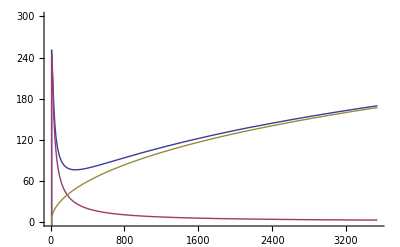

```mathematica
gr1=ListPlot[{datadEdxtotvsE,datadEdxivsE,datadEdxevsE},Joined-> True,PlotRange-> {0,0.3*10^3}]
```

### interpolating functions for dE/dx

```mathematica
dEdxE=Interpolation[datadEdxtotvsE];
dEdxiE=Interpolation[datadEdxivsE];
dEdxeE=Interpolation[datadEdxevsE];
```

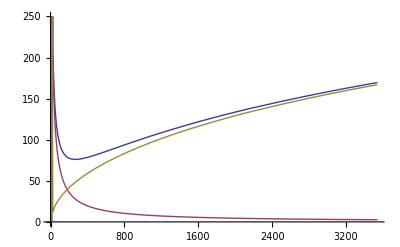

```mathematica
gr2=Plot[{dEdxE[EE],dEdxiE[EE],dEdxeE[EE]},{EE,0,E0},PlotRange-> {0,0.25*10^3}]
```

```mathematica
(* Show[gr1,gr2] *)
```

### Range: E=E(x)

```mathematica
dxE[e_] :=1/dEdxE[e]
xE[e_]   := NIntegrate[1/dEdxE[Ep],{Ep,e,E0},PrecisionGoal->Automatic]
```

```mathematica
Nmax=100;
emin=1.5*Te;
emax=E0;
dE=(emax-emin)/Nmax;
dataEx=Table[{xE[e],e},{e,emin,emax,dE}] (* Convert dE/dx from MeV/μm to keV/μm *)
dataEx[[1]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Ep near {Ep} = {25.15978235660914`}. NIntegrate obtained 29.7989 and 0.00187739 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{29.7989,4.5},{29.708,39.855},{29.4289,75.21},{29.0688,110.565},{28.659,145.92},{28.2199,181.275},{27.7649,216.63},{27.3024,251.985},{26.8378,287.34},{26.3747,322.695},{25.9152,358.05},{25.4609,393.405},{25.0126,428.76},{24.5707,464.115},{24.1357,499.47},{23.7075,534.825},{23.2861,570.18},{22.8715,605.535},{22.4636,640.89},{22.0621,676.245},{21.6669,711.6},{21.2777,746.955},{20.8944,782.31},{20.5168,817.665},{20.1447,853.02},{19.7778,888.375},{19.4161,923.73},{19.0592,959.085},{18.7071,994.44},{18.3595,1029.8},{18.0164,1065.15},{17.6775,1100.51},{17.3427,1135.86},{17.0119,1171.22},{16.6849,1206.57},{16.3617,1241.93},{16.042,1277.28},{15.7258,1312.64},{15.4129,1347.99},{15.1034,1383.35},{14.7969,1418.7},{14.4936,1454.06},{14.1932,1489.41},{13.8957,1524.77},{13.6009,1560.12},{13.309,1595.48},{13.0196,1630.83},{12.7328,1666.19},{12.4486,1701.54},{12.1667,1736.9},{11.8873,1772.25},{11.6101,1807.61},{11.3352,1842.96},{11.0625,1878.32},{10.7919,1913.67},{10.5234,1949.03},{10.257,1984.38},{9.9925,2019.74},{9.72997,2055.09},{9.46934,2090.45},{9.21056,2125.8},{8.95358,2161.16},{8.69842,2196.51},{8.44463,2231.87},{8.19252,2267.22},{7.94207,2302.58},{7.69322,2337.93},{7.44596,2373.29},{7.20024,2408.64},{6.95603,2444.},{6.71331,2479.35},{6.47204,2514.71},{6.23219,2550.06},{5.99374,2585.42},{5.75665,2620.77},{5.52091,2656.13},{5.28649,2691.48},{5.05335,2726.84},{4.82149,2762.19},{4.59086,2797.55},{4.36146,2832.9},{4.13326,2868.26},{3.90624,2903.61},{3.68037,2938.97},{3.45565,2974.32},{3.23203,3009.68},{3.00952,3045.03},{2.78809,3080.39},{2.56771,3115.74},{2.34839,3151.1},{2.13008,3186.45},{1.91279,3221.81},{1.69649,3257.16},{1.48116,3292.52},{1.2668,3327.87},{1.05339,3363.23},{0.840903,3398.58},{0.629337,3433.94},{0.418673,3469.29},{0.208899,3504.65},{-2.68134×10^-15,3540.}}

{29.7989,4.5}

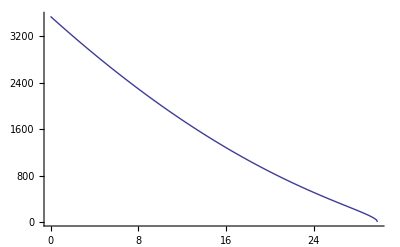

29.7989

```mathematica
gr3=ListPlot[dataEx,Joined-> True] (* microns *)
dataEx[[1,1]]
```

### check range consistency with range.f90

```mathematica
nts=99; (* stop reading when Ep goes critical,
            in this case when Ep < 0 *)st=OpenRead["range.001.out"];
Do[Read[st,String],{i,1,19}];
ne=Read[st,Number];
Te=Read[st,Number];
Ti=Read[st,Number];
{Te,Ti,ne}
nn=Read[st,{Number,Number,Number}]
proj=Read[st,{Number,Number,Number}]
data=
Table[Read[st,{Number,Number,Number,Number,Number,Number,Number,Number}],{i,1,nts}];
Close[st];
data;
```

{3.,3.,1.×10^25}

{1.×10^-11,100,10}

{3540.,3.75309×10^6,2.}

```mathematica
scale2=10^4; (* cm to μm *)
Evsx=Table[{data[[i,3]]*scale2,data[[i,5]]},{i,1,nts}];data1=Table[{data[[i,3]],data[[i,6]]},{i,1,nts}];
data2=Table[{data[[i,3]],data[[i,7]]},{i,1,nts}];data3=Table[{data[[i,3]],data[[i,8]]},{i,1,nts}];
data[[44,3]]*10^4
```

29.2504

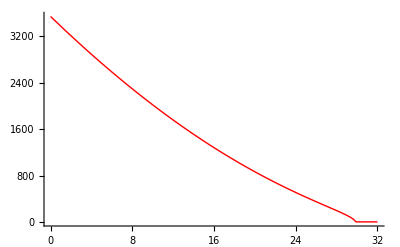

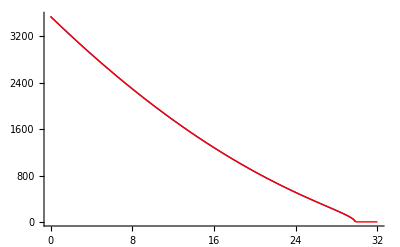

```mathematica
gr4b=ListPlot[Evsx,Joined-> True,PlotStyle-> Red]
Show[gr3,gr4b] (* a simple scaling of E *)
```

## Te=30 keV Ti= 30keV ne=10^25cm^-3 α projectile: 002

### plotting dE/dx vs E from dedx.out file

```mathematica
st=OpenRead["dedx.002.out"];
Do[Read[st,String],{i,1,19}];
ne=Read[st,Number]
Te=Read[st,Number]
Ti=Read[st,Number]
nn=Read[st,Number]
proj=Read[st,{Number,Number,Number}]
nts=nn+1; (* stop reading when Ep goes critical,
            in this case when Ep < 0 *)
data=
Table[Read[st,{Number,Number,Number,Number,Number}],{i,1,nts}];
Close[st];
data
```

1.×10^25

30.

30.

300

{3540.,3.75309×10^6,2.}

{{0,0.00001,-195.294,-193.143,-2.15138},{1,11.8,-0.104177,-0.102685,-0.00149217},{2,23.6,-0.0317115,-0.0310122,-0.000699295},{3,35.4,0.000536692,0.000809127,-0.000272435},{4,47.2,0.0190796,0.0190507,0.000028901},{5,59.,0.0300682,0.0298005,0.000267682},{6,70.8,0.0366,0.0361311,0.00046894},{7,82.6,0.0403141,0.0396692,0.000644913},{8,94.4,0.0422805,0.0414781,0.000802402},{9,106.2,0.0431199,0.0421744,0.000945564},{10,118.,0.043159,0.0420819,0.00107715},{11,129.8,0.0429048,0.0417057,0.0011991},{12,141.6,0.0422577,0.0409448,0.00131288},{13,153.4,0.041382,0.0399624,0.00141964},{14,165.2,0.0403831,0.0388628,0.00152029},{15,177.,0.0393178,0.0377022,0.00161561},{16,188.8,0.0382032,0.036497,0.00170622},{17,200.6,0.037114,0.0353214,0.00179267},{18,212.4,0.0360446,0.0341692,0.0018754},{19,224.2,0.0350032,0.0330484,0.00195481},{20,236.,0.033998,0.0319668,0.00203123},{21,247.8,0.0330336,0.0309286,0.00210494},{22,259.6,0.0321123,0.0299361,0.00217619},{23,271.4,0.0312349,0.0289897,0.0022452},{24,283.2,0.0303803,0.0280681,0.00231215},{25,295.,0.0295932,0.027216,0.00237722},{26,306.8,0.0288465,0.0264059,0.00244054},{27,318.6,0.0281384,0.0256362,0.00250225},{28,330.4,0.0274673,0.0249048,0.00256246},{29,342.2,0.0268313,0.02421,0.00262127},{30,354.,0.0262284,0.0235497,0.00267877},{31,365.8,0.0256569,0.0229218,0.00273506},{32,377.6,0.0251148,0.0223246,0.00279019},{33,389.4,0.0246004,0.0217562,0.00284424},{34,401.2,0.024112,0.0212148,0.00289727},{35,413.,0.0236481,0.0206987,0.00294933},{36,424.8,0.023207,0.0202066,0.00300048},{37,436.6,0.0227875,0.0197367,0.00305076},{38,448.4,0.0223881,0.0192879,0.00310022},{39,460.2,0.0220077,0.0188588,0.00314889},{40,472.,0.0216451,0.0184483,0.00319681},{41,483.8,0.0212992,0.0180552,0.00324401},{42,495.6,0.020969,0.0176784,0.00329053},{43,507.4,0.0206536,0.0173172,0.0033364},{44,519.2,0.0203521,0.0169704,0.00338163},{45,531.,0.0200637,0.0166374,0.00342627},{46,542.8,0.0197876,0.0163173,0.00347032},{47,554.6,0.0195233,0.0160095,0.00351381},{48,566.4,0.0192699,0.0157131,0.00355677},{49,578.2,0.019027,0.0154277,0.00359921},{50,590.,0.0187938,0.0151527,0.00364115},{51,601.8,0.01857,0.0148874,0.0036826},{52,613.6,0.018355,0.0146315,0.0037236},{53,625.4,0.0181484,0.0143843,0.00376413},{54,637.2,0.0179497,0.0141455,0.00380424},{55,649.,0.0177586,0.0139147,0.00384392},{56,660.8,0.0175746,0.0136914,0.00388319},{57,672.6,0.0173974,0.0134753,0.00392206},{58,684.4,0.0172266,0.0132661,0.00396055},{59,696.2,0.017062,0.0130634,0.00399866},{60,708.,0.0169033,0.0128669,0.00403641},{61,719.8,0.0167502,0.0126764,0.00407381},{62,731.6,0.0166024,0.0124916,0.00411086},{63,743.4,0.0164597,0.0123122,0.00414758},{64,755.2,0.0163219,0.012138,0.00418397},{65,767.,0.0161888,0.0119687,0.00422005},{66,778.8,0.0160601,0.0118042,0.00425581},{67,790.6,0.0159356,0.0116443,0.00429128},{68,802.4,0.0158153,0.0114888,0.00432645},{69,814.2,0.0156988,0.0113375,0.00436133},{70,826.,0.0155861,0.0111902,0.00439593},{71,837.8,0.015477,0.0110467,0.00443026},{72,849.6,0.0153713,0.010907,0.00446432},{73,861.4,0.0152689,0.0107708,0.00449812},{74,873.2,0.0151698,0.0106381,0.00453167},{75,885.,0.0150736,0.0105087,0.00456496},{76,896.8,0.0149805,0.0103824,0.00459802},{77,908.6,0.0148901,0.0102593,0.00463083},{78,920.4,0.0148025,0.0101391,0.00466341},{79,932.2,0.0147175,0.0100217,0.00469575},{80,944.,0.014635,0.00990709,0.00472788},{81,955.8,0.0145549,0.00979513,0.00475978},{82,967.6,0.0144772,0.00968573,0.00479147},{83,979.4,0.0144018,0.0095788,0.00482295},{84,991.2,0.0143285,0.00947427,0.00485422},{85,1003.,0.0142573,0.00937204,0.00488529},{86,1014.8,0.0141882,0.00927205,0.00491616},{87,1026.6,0.014121,0.00917422,0.00494683},{88,1038.4,0.0140558,0.00907848,0.00497731},{89,1050.2,0.0139924,0.00898476,0.0050076},{90,1062.,0.0139307,0.008893,0.0050377},{91,1073.8,0.0138708,0.00880315,0.00506763},{92,1085.6,0.0138125,0.00871513,0.00509737},{93,1097.4,0.0137558,0.00862889,0.00512694},{94,1109.2,0.0137007,0.00854438,0.00515634},{95,1121.,0.0136471,0.00846156,0.00518556},{96,1132.8,0.013595,0.00838035,0.00521462},{97,1144.6,0.0135443,0.00830073,0.00524352},{98,1156.4,0.0134949,0.00822264,0.00527226},{99,1168.2,0.0134469,0.00814604,0.00530083},{100,1180.,0.0134001,0.00807089,0.00532925},{101,1191.8,0.0133547,0.00799714,0.00535752},{102,1203.6,0.0133101,0.00792449,0.00538564},{103,1215.4,0.0132671,0.00785345,0.00541361},{104,1227.2,0.0132251,0.00778369,0.00544143},{105,1239.,0.0131843,0.00771519,0.0054691},{106,1250.8,0.0131446,0.00764792,0.00549664},{107,1262.6,0.0131059,0.00758183,0.00552403},{108,1274.4,0.0130682,0.0075169,0.00555129},{109,1286.2,0.0130315,0.0074531,0.00557841},{110,1298.,0.0129958,0.0073904,0.00560539},{111,1309.8,0.012961,0.00732877,0.00563225},{112,1321.6,0.0129272,0.00726818,0.00565897},{113,1333.4,0.0128942,0.00720861,0.00568557},{114,1345.2,0.0128621,0.00715003,0.00571204},{115,1357.,0.0128308,0.00709241,0.00573839},{116,1368.8,0.0128003,0.00703574,0.00576461},{117,1380.6,0.0127707,0.00697998,0.00579071},{118,1392.4,0.0127418,0.00692513,0.00581669},{119,1404.2,0.0127137,0.00687114,0.00584255},{120,1416.,0.0126863,0.00681802,0.0058683},{121,1427.8,0.0126596,0.00676572,0.00589393},{122,1439.6,0.0126337,0.00671424,0.00591945},{123,1451.4,0.0126084,0.00666356,0.00594485},{124,1463.2,0.0125838,0.00661365,0.00597015},{125,1475.,0.0125598,0.0065645,0.00599533},{126,1486.8,0.0125365,0.00651609,0.00602041},{127,1498.6,0.0125138,0.0064684,0.00604538},{128,1510.4,0.0124917,0.00642143,0.00607025},{129,1522.2,0.0124702,0.00637515,0.00609501},{130,1534.,0.0124492,0.00632954,0.00611967},{131,1545.8,0.0124288,0.0062846,0.00614422},{132,1557.6,0.012409,0.0062403,0.00616868},{133,1569.4,0.0123897,0.00619664,0.00619304},{134,1581.2,0.0123709,0.0061536,0.00621729},{135,1593.,0.0123526,0.00611117,0.00624146},{136,1604.8,0.0123349,0.00606933,0.00626552},{137,1616.6,0.0123176,0.00602807,0.0062895},{138,1628.4,0.0123008,0.00598738,0.00631337},{139,1640.2,0.0122844,0.00594725,0.00633716},{140,1652.,0.0122685,0.00590767,0.00636086},{141,1663.8,0.0122531,0.00586862,0.00638446},{142,1675.6,0.0122381,0.00583009,0.00640798},{143,1687.4,0.0122235,0.00579208,0.0064314},{144,1699.2,0.0122093,0.00575458,0.00645474},{145,1711.,0.0121956,0.00571756,0.00647799},{146,1722.8,0.0121822,0.00568103,0.00650116},{147,1734.6,0.0121692,0.00564497,0.00652424},{148,1746.4,0.0121566,0.00560938,0.00654724},{149,1758.2,0.0121444,0.00557425,0.00657016},{150,1770.,0.0121326,0.00553956,0.00659299},{151,1781.8,0.0121211,0.00550531,0.00661575},{152,1793.6,0.0121099,0.00547149,0.00663842},{153,1805.4,0.0120989,0.00543785,0.00666101},{154,1817.2,0.0120884,0.00540487,0.00668353},{155,1829.,0.0120783,0.00537229,0.00670596},{156,1840.8,0.0120684,0.00534012,0.00672832},{157,1852.6,0.0120589,0.00530833,0.00675061},{158,1864.4,0.0120498,0.00527693,0.00677282},{159,1876.2,0.0120409,0.00524591,0.00679495},{160,1888.,0.0120323,0.00521526,0.00681701},{161,1899.8,0.012024,0.00518497,0.00683899},{162,1911.6,0.0120159,0.00515504,0.0068609},{163,1923.4,0.0120082,0.00512546,0.00688275},{164,1935.2,0.0120007,0.00509623,0.00690451},{165,1947.,0.0119935,0.00506734,0.00692621},{166,1958.8,0.0119866,0.00503877,0.00694784},{167,1970.6,0.0119799,0.00501054,0.0069694},{168,1982.4,0.0119735,0.00498262,0.00699089},{169,1994.2,0.0119673,0.00495503,0.00701231},{170,2006.,0.0119614,0.00492774,0.00703367},{171,2017.8,0.0119557,0.00490076,0.00705496},{172,2029.6,0.0119503,0.00487408,0.00707618},{173,2041.4,0.011945,0.00484769,0.00709734},{174,2053.2,0.01194,0.0048216,0.00711843},{175,2065.,0.0119352,0.00479579,0.00713945},{176,2076.8,0.0119307,0.00477026,0.00716042},{177,2088.6,0.0119263,0.004745,0.00718132},{178,2100.4,0.0119222,0.00472002,0.00720215},{179,2112.2,0.0119182,0.00469531,0.00722293},{180,2124.,0.0119145,0.00467086,0.00724364},{181,2135.8,0.011911,0.00464667,0.00726429},{182,2147.6,0.0119076,0.00462273,0.00728488},{183,2159.4,0.0119045,0.00459904,0.00730541},{184,2171.2,0.0119015,0.0045756,0.00732589},{185,2183.,0.0118987,0.00455241,0.0073463},{186,2194.8,0.0118961,0.00452945,0.00736665},{187,2206.6,0.0118937,0.00450673,0.00738695},{188,2218.4,0.0118914,0.00448424,0.00740718},{189,2230.2,0.0118893,0.00446197,0.00742736},{190,2242.,0.0118874,0.00443994,0.00744749},{191,2253.8,0.0118857,0.00441812,0.00746755},{192,2265.6,0.0118841,0.00439652,0.00748757},{193,2277.4,0.0118827,0.00437514,0.00750752},{194,2289.2,0.0118814,0.00435396,0.00752742},{195,2301.,0.0118803,0.004333,0.00754727},{196,2312.8,0.0118793,0.00431224,0.00756706},{197,2324.6,0.0118785,0.00429169,0.0075868},{198,2336.4,0.0118778,0.00427133,0.00760648},{199,2348.2,0.0118773,0.00425117,0.00762612},{200,2360.,0.0118769,0.0042312,0.0076457},{201,2371.8,0.0118766,0.00421142,0.00766523},{202,2383.6,0.0118765,0.00419183,0.0076847},{203,2395.4,0.0118766,0.00417243,0.00770413},{204,2407.2,0.0118767,0.00415321,0.0077235},{205,2419.,0.011877,0.00413417,0.00774283},{206,2430.8,0.0118774,0.00411531,0.0077621},{207,2442.6,0.0118779,0.00409662,0.00778132},{208,2454.4,0.0118786,0.0040781,0.0078005},{209,2466.2,0.0118794,0.00405976,0.00781962},{210,2478.,0.0118803,0.00404158,0.0078387},{211,2489.8,0.0118813,0.00402357,0.00785773},{212,2501.6,0.0118824,0.00400572,0.00787671},{213,2513.4,0.0118837,0.00398803,0.00789564},{214,2525.2,0.011885,0.0039705,0.00791453},{215,2537.,0.0118865,0.00395313,0.00793337},{216,2548.8,0.0118881,0.00393591,0.00795216},{217,2560.6,0.0118898,0.00391885,0.00797091},{218,2572.4,0.0118915,0.00390193,0.00798961},{219,2584.2,0.0118934,0.00388517,0.00800826},{220,2596.,0.0118954,0.00386855,0.00802687},{221,2607.8,0.0118975,0.00385207,0.00804544},{222,2619.6,0.0118997,0.00383574,0.00806396},{223,2631.4,0.011902,0.00381955,0.00808243},{224,2643.2,0.0119044,0.0038035,0.00810086},{225,2655.,0.0119068,0.00378758,0.00811925},{226,2666.8,0.0119094,0.0037718,0.00813759},{227,2678.6,0.011912,0.00375615,0.0081559},{228,2690.4,0.0119148,0.00374064,0.00817415},{229,2702.2,0.0119176,0.00372526,0.00819237},{230,2714.,0.0119205,0.00371,0.00821054},{231,2725.8,0.0119235,0.00369487,0.00822867},{232,2737.6,0.0119266,0.00367987,0.00824676},{233,2749.4,0.0119298,0.00366499,0.00826481},{234,2761.2,0.0119331,0.00365024,0.00828282},{235,2773.,0.0119364,0.0036356,0.00830078},{236,2784.8,0.0119398,0.00362109,0.00831871},{237,2796.6,0.0119433,0.00360669,0.00833659},{238,2808.4,0.0119468,0.00359241,0.00835444},{239,2820.2,0.0119505,0.00357824,0.00837224},{240,2832.,0.0119542,0.00356419,0.00839001},{241,2843.8,0.011958,0.00355025,0.00840773},{242,2855.6,0.0119618,0.00353642,0.00842542},{243,2867.4,0.0119658,0.0035227,0.00844307},{244,2879.2,0.0119698,0.00350909,0.00846068},{245,2891.,0.0119738,0.00349558,0.00847825},{246,2902.8,0.011978,0.00348218,0.00849578},{247,2914.6,0.0119822,0.00346889,0.00851328},{248,2926.4,0.0119864,0.0034557,0.00853073},{249,2938.2,0.0119908,0.00344261,0.00854815},{250,2950.,0.0119952,0.00342962,0.00856554},{251,2961.8,0.0119996,0.00341673,0.00858288},{252,2973.6,0.0120041,0.00340394,0.00860019},{253,2985.4,0.0120087,0.00339125,0.00861746},{254,2997.2,0.0120133,0.00337865,0.0086347},{255,3009.,0.012018,0.00336615,0.0086519},{256,3020.8,0.0120228,0.00335374,0.00866906},{257,3032.6,0.0120276,0.00334143,0.00868619},{258,3044.4,0.0120325,0.00332921,0.00870328},{259,3056.2,0.0120374,0.00331708,0.00872034},{260,3068.,0.0120424,0.00330503,0.00873736},{261,3079.8,0.0120474,0.00329308,0.00875435},{262,3091.6,0.0120525,0.00328122,0.0087713},{263,3103.4,0.0120577,0.00326944,0.00878822},{264,3115.2,0.0120629,0.00325775,0.0088051},{265,3127.,0.0120681,0.00324614,0.00882195},{266,3138.8,0.0120734,0.00323462,0.00883877},{267,3150.6,0.0120787,0.00322318,0.00885555},{268,3162.4,0.0120841,0.00321183,0.0088723},{269,3174.2,0.0120896,0.00320055,0.00888901},{270,3186.,0.0120951,0.00318936,0.0089057},{271,3197.8,0.0121006,0.00317824,0.00892234},{272,3209.6,0.0121062,0.00316721,0.00893896},{273,3221.4,0.0121118,0.00315625,0.00895555},{274,3233.2,0.0121175,0.00314537,0.0089721},{275,3245.,0.0121232,0.00313456,0.00898862},{276,3256.8,0.0121289,0.00312383,0.0090051},{277,3268.6,0.0121347,0.00311318,0.00902156},{278,3280.4,0.0121406,0.0031026,0.00903798},{279,3292.2,0.0121465,0.00309209,0.00905438},{280,3304.,0.0121524,0.00308166,0.00907074},{281,3315.8,0.0121584,0.00307129,0.00908707},{282,3327.6,0.0121644,0.003061,0.00910337},{283,3339.4,0.0121704,0.00305078,0.00911964},{284,3351.2,0.0121765,0.00304063,0.00913587},{285,3363.,0.0121826,0.00303054,0.00915208},{286,3374.8,0.0121888,0.00302053,0.00916826},{287,3386.6,0.012195,0.00301058,0.0091844},{288,3398.4,0.0122012,0.0030007,0.00920052},{289,3410.2,0.0122075,0.00299088,0.00921661},{290,3422.,0.0122138,0.00298113,0.00923266},{291,3433.8,0.0122201,0.00297145,0.00924869},{292,3445.6,0.0122265,0.00296183,0.00926469},{293,3457.4,0.0122329,0.00295227,0.00928066},{294,3469.2,0.0122394,0.00294277,0.0092966},{295,3481.,0.0122458,0.00293334,0.00931251},{296,3492.8,0.0122524,0.00292397,0.00932839},{297,3504.6,0.0122589,0.00291466,0.00934424},{298,3516.4,0.0122655,0.00290541,0.00936007},{299,3528.2,0.0122721,0.00289622,0.00937587},{300,3540.,0.0122787,0.00288708,0.00939163}}

```mathematica
datadEdxtotvsE=Table[{data[[i,2]],data[[i,3]]*10^3},{i,1,nts}];
datadEdxivsE=Table[{data[[i,2]],data[[i,4]]*10^3},{i,1,nts}];datadEdxevsE=Table[{data[[i,2]],data[[i,5]]*10^3},{i,1,nts}];
E0=datadEdxtotvsE[[nts,1]]
(* convert from MeV/μm to keV/μm *)
```

3540.

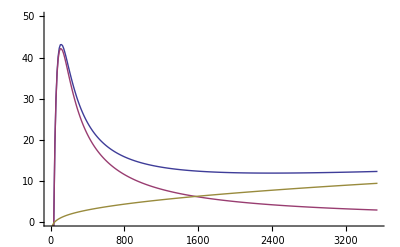

```mathematica
gr1=ListPlot[{datadEdxtotvsE,datadEdxivsE,datadEdxevsE},Joined-> True,PlotRange-> {0,0.05*10^3}]
```

### interpolating functions for dE/dx

```mathematica
dEdxE=Interpolation[datadEdxtotvsE];
dEdxiE=Interpolation[datadEdxivsE];
dEdxeE=Interpolation[datadEdxevsE];
```

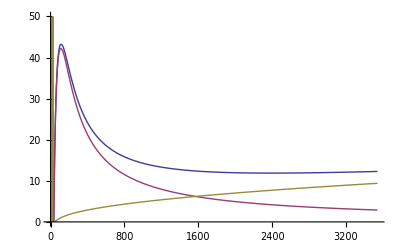

```mathematica
gr2=Plot[{dEdxE[EE],dEdxiE[EE],dEdxeE[EE]},{EE,0,E0},PlotRange-> {0,0.05*10^3}]
```

```mathematica
(* Show[gr1,gr2] *)
```

### Range: E=E(x)

```mathematica
dxE[e_] :=1/dEdxE[e]
xE[e_]   := NIntegrate[1/dEdxE[Ep],{Ep,e,E0},PrecisionGoal->Automatic]
```

```mathematica
Nmax=100;
emin=1.5*Te;
emax=E0;
dE=(emax-emin)/Nmax;
dataEx=Table[{xE[e],e},{e,emin,emax,dE}] (* Convert dE/dx from MeV/μm to keV/μm *)
dataEx[[1]]
```

{{252.904,45.},{251.71,79.95},{250.881,114.9},{250.062,149.85},{249.191,184.8},{248.245,219.75},{247.214,254.7},{246.093,289.65},{244.88,324.6},{243.578,359.55},{242.188,394.5},{240.713,429.45},{239.156,464.4},{237.519,499.35},{235.807,534.3},{234.022,569.25},{232.169,604.2},{230.25,639.15},{228.269,674.1},{226.228,709.05},{224.131,744.},{221.981,778.95},{219.779,813.9},{217.53,848.85},{215.235,883.8},{212.896,918.75},{210.517,953.7},{208.099,988.65},{205.645,1023.6},{203.156,1058.55},{200.634,1093.5},{198.082,1128.45},{195.5,1163.4},{192.891,1198.35},{190.257,1233.3},{187.598,1268.25},{184.916,1303.2},{182.213,1338.15},{179.49,1373.1},{176.748,1408.05},{173.989,1443.},{171.213,1477.95},{168.421,1512.9},{165.615,1547.85},{162.796,1582.8},{159.964,1617.75},{157.121,1652.7},{154.266,1687.65},{151.402,1722.6},{148.529,1757.55},{145.647,1792.5},{142.757,1827.45},{139.861,1862.4},{136.957,1897.35},{134.048,1932.3},{131.134,1967.25},{128.215,2002.2},{125.291,2037.15},{122.364,2072.1},{119.433,2107.05},{116.5,2142.},{113.564,2176.95},{110.626,2211.9},{107.687,2246.85},{104.746,2281.8},{101.804,2316.75},{98.8615,2351.7},{95.9188,2386.65},{92.976,2421.6},{90.0336,2456.55},{87.0916,2491.5},{84.1505,2526.45},{81.2104,2561.4},{78.2716,2596.35},{75.3343,2631.3},{72.3987,2666.25},{69.465,2701.2},{66.5334,2736.15},{63.6041,2771.1},{60.6772,2806.05},{57.7528,2841.},{54.8313,2875.95},{51.9126,2910.9},{48.997,2945.85},{46.0846,2980.8},{43.1754,3015.75},{40.2697,3050.7},{37.3674,3085.65},{34.4688,3120.6},{31.574,3155.55},{28.6829,3190.5},{25.7958,3225.45},{22.9126,3260.4},{20.0336,3295.35},{17.1587,3330.3},{14.288,3365.25},{11.4216,3400.2},{8.55949,3435.15},{5.70185,3470.1},{2.84866,3505.05},{-3.70354×10^-14,3540.}}

{252.904,45.}

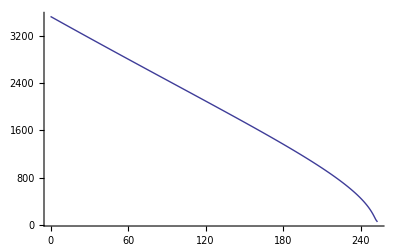

252.904

```mathematica
gr3=ListPlot[dataEx,Joined-> True] (* microns *)
dataEx[[1,1]]
```

### check range consistency with range.f90

```mathematica
nts=99; (* stop reading when Ep goes critical,
            in this case when Ep < 0 *)st=OpenRead["range.002.out"];
Do[Read[st,String],{i,1,19}];
ne=Read[st,Number];
Te=Read[st,Number];
Ti=Read[st,Number];
{Te,Ti,ne}
nn=Read[st,{Number,Number,Number}]
proj=Read[st,{Number,Number,Number}]
data=
Table[Read[st,{Number,Number,Number,Number,Number,Number,Number,Number}],{i,1,nts}];
Close[st];
data;
```

{30.,30.,1.×10^25}

{6.×10^-11,100,10}

{3540.,3.75309×10^6,2.}

```mathematica
scale2=10^4; (* cm to μm *)
Evsx=Table[{data[[i,3]]*scale2,data[[i,5]]},{i,1,nts}];data1=Table[{data[[i,3]],data[[i,6]]},{i,1,nts}];
data2=Table[{data[[i,3]],data[[i,7]]},{i,1,nts}];data3=Table[{data[[i,3]],data[[i,8]]},{i,1,nts}];
data[[44,3]]*10^4
```

237.955

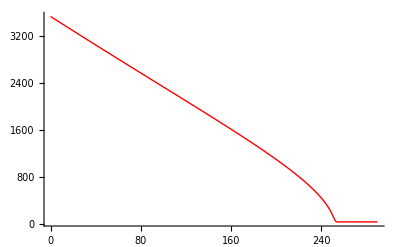

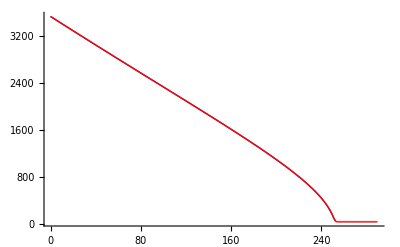

```mathematica
gr4b=ListPlot[Evsx,Joined-> True,PlotStyle-> Red]
Show[gr3,gr4b] (* a simple scaling of E *)
```

## FF: case 3 [range of FF in DT]: 003

### plotting dE/dx vs E from dedx.out file

```mathematica
st=OpenRead["dedx.003.out"];
Do[Read[st,String],{i,1,19}];
ne=Read[st,Number]
Te=Read[st,Number]
Ti=Read[st,Number]
nn=Read[st,Number]
proj=Read[st,{Number,Number,Number}]
nts=nn+1; (* stop reading when Ep goes critical,
            in this case when Ep < 0 *)
data=
Table[Read[st,{Number,Number,Number,Number,Number}],{i,1,nts}];
Close[st];
data
```

1.×10^23

1.

1.

300

{92500.,1.12593×10^8,25.}

{{0,0.00001,-101.245,-99.7587,-1.48669},{1,308.333,0.690711,0.626074,0.0646364},{2,616.667,0.464085,0.373546,0.0905389},{3,925.,0.37954,0.269259,0.110281},{4,1233.33,0.339169,0.212239,0.12693},{5,1541.67,0.317654,0.176053,0.141602},{6,1850.,0.305778,0.150915,0.154863},{7,2158.33,0.299438,0.132384,0.167054},{8,2466.67,0.296513,0.118118,0.178395},{9,2775.,0.295815,0.106775,0.189039},{10,3083.33,0.296626,0.0975273,0.199099},{11,3391.67,0.298492,0.0898334,0.208658},{12,3700.,0.30111,0.0833261,0.217784},{13,4008.33,0.304274,0.077746,0.226528},{14,4316.67,0.307838,0.0729047,0.234934},{15,4625.,0.311698,0.0686623,0.243035},{16,4933.33,0.315775,0.0649121,0.250863},{17,5241.67,0.320014,0.0615717,0.258442},{18,5550.,0.324369,0.0585762,0.265793},{19,5858.33,0.328809,0.055874,0.272934},{20,6166.67,0.333306,0.0534232,0.279883},{21,6475.,0.337842,0.0511896,0.286652},{22,6783.33,0.3424,0.0491452,0.293254},{23,7091.67,0.346968,0.0472663,0.299701},{24,7400.,0.351536,0.0455334,0.306002},{25,7708.33,0.356096,0.0439298,0.312166},{26,8016.67,0.360642,0.0424412,0.318201},{27,8325.,0.36517,0.0410555,0.324114},{28,8633.33,0.369675,0.0397621,0.329913},{29,8941.67,0.374154,0.0385521,0.335602},{30,9250.,0.378604,0.0374174,0.341187},{31,9558.33,0.383025,0.0363511,0.346674},{32,9866.67,0.387413,0.0353471,0.352066},{33,10175.,0.391769,0.0343999,0.357369},{34,10483.3,0.396091,0.0335049,0.362586},{35,10791.7,0.400379,0.0326576,0.367722},{36,11100.,0.404632,0.0318544,0.372778},{37,11408.3,0.408851,0.0310919,0.377759},{38,11716.7,0.413034,0.0303669,0.382667},{39,12025.,0.417183,0.0296766,0.387506},{40,12333.3,0.421296,0.0290187,0.392278},{41,12641.7,0.425375,0.0283909,0.396984},{42,12950.,0.42942,0.0277911,0.401629},{43,13258.3,0.433431,0.0272174,0.406213},{44,13566.7,0.437407,0.0266681,0.410739},{45,13875.,0.441351,0.0261417,0.415209},{46,14183.3,0.445261,0.0256368,0.419624},{47,14491.7,0.449139,0.025152,0.423987},{48,14800.,0.452985,0.0246862,0.428298},{49,15108.3,0.456798,0.0242381,0.43256},{50,15416.7,0.460581,0.0238069,0.436774},{51,15725.,0.464333,0.0233916,0.440941},{52,16033.3,0.468054,0.0229913,0.445063},{53,16341.7,0.471746,0.0226051,0.449141},{54,16650.,0.475408,0.0222323,0.453176},{55,16958.3,0.479041,0.0218723,0.457169},{56,17266.7,0.482645,0.0215243,0.461121},{57,17575.,0.486222,0.0211879,0.465034},{58,17883.3,0.489771,0.0208623,0.468908},{59,18191.7,0.493292,0.020547,0.472745},{60,18500.,0.496787,0.0202417,0.476545},{61,18808.3,0.500255,0.0199457,0.480309},{62,19116.7,0.503698,0.0196587,0.484039},{63,19425.,0.507114,0.0193803,0.487734},{64,19733.3,0.510506,0.0191101,0.491396},{65,20041.7,0.513873,0.0188476,0.495025},{66,20350.,0.517215,0.0185927,0.498623},{67,20658.3,0.520534,0.0183449,0.502189},{68,20966.7,0.523829,0.018104,0.505725},{69,21275.,0.527101,0.0178696,0.509231},{70,21583.3,0.530349,0.0176415,0.512708},{71,21891.7,0.533576,0.0174195,0.516156},{72,22200.,0.535972,0.0172032,0.518769},{73,22508.3,0.539127,0.0169926,0.522134},{74,22816.7,0.542259,0.0167872,0.525471},{75,23125.,0.545369,0.0165871,0.528782},{76,23433.3,0.548458,0.0163919,0.532066},{77,23741.7,0.551526,0.0162015,0.535324},{78,24050.,0.554573,0.0160156,0.538557},{79,24358.3,0.557599,0.0158342,0.541765},{80,24666.7,0.560605,0.0156571,0.544948},{81,24975.,0.563591,0.0154841,0.548107},{82,25283.3,0.566558,0.015315,0.551243},{83,25591.7,0.569505,0.0151498,0.554355},{84,25900.,0.572432,0.0149883,0.557444},{85,26208.3,0.575341,0.0148304,0.560511},{86,26516.7,0.578231,0.0146759,0.563555},{87,26825.,0.581103,0.0145248,0.566578},{88,27133.3,0.583956,0.0143769,0.569579},{89,27441.7,0.586792,0.0142321,0.57256},{90,27750.,0.589609,0.0140904,0.575519},{91,28058.3,0.59241,0.0139516,0.578458},{92,28366.7,0.595193,0.0138157,0.581377},{93,28675.,0.597959,0.0136825,0.584276},{94,28983.3,0.600708,0.013552,0.587156},{95,29291.7,0.60344,0.013424,0.590016},{96,29600.,0.606156,0.0132986,0.592857},{97,29908.3,0.608856,0.0131756,0.59568},{98,30216.7,0.611539,0.013055,0.598484},{99,30525.,0.614207,0.0129367,0.601271},{100,30833.3,0.616859,0.0128206,0.604039},{101,31141.7,0.619496,0.0127067,0.606789},{102,31450.,0.622117,0.0125949,0.609523},{103,31758.3,0.624724,0.0124851,0.612239},{104,32066.7,0.627315,0.0123773,0.614938},{105,32375.,0.629892,0.0122715,0.61762},{106,32683.3,0.632454,0.0121675,0.620286},{107,32991.7,0.635001,0.0120654,0.622936},{108,33300.,0.637535,0.0119651,0.62557},{109,33608.3,0.640054,0.0118665,0.628187},{110,33916.7,0.642559,0.0117695,0.630789},{111,34225.,0.64505,0.0116743,0.633376},{112,34533.3,0.647528,0.0115806,0.635948},{113,34841.7,0.649992,0.0114885,0.638504},{114,35150.,0.652443,0.0113979,0.641045},{115,35458.3,0.654881,0.0113089,0.643572},{116,35766.7,0.657305,0.0112212,0.646084},{117,36075.,0.659717,0.011135,0.648582},{118,36383.3,0.662115,0.0110502,0.651065},{119,36691.7,0.664501,0.0109667,0.653535},{120,37000.,0.666875,0.0108845,0.65599},{121,37308.3,0.669236,0.0108036,0.658432},{122,37616.7,0.671584,0.0107239,0.66086},{123,37925.,0.673921,0.0106455,0.663275},{124,38233.3,0.676245,0.0105683,0.665677},{125,38541.7,0.678558,0.0104922,0.668066},{126,38850.,0.680858,0.0104173,0.670441},{127,39158.3,0.683147,0.0103435,0.672804},{128,39466.7,0.685425,0.0102708,0.675154},{129,39775.,0.68804,0.0101991,0.677841},{130,40083.3,0.6903,0.0101285,0.680171},{131,40391.7,0.692549,0.0100589,0.68249},{132,40700.,0.694787,0.00999029,0.684796},{133,41008.3,0.697014,0.00992267,0.687091},{134,41316.7,0.69923,0.009856,0.689374},{135,41625.,0.701435,0.00979026,0.691645},{136,41933.3,0.703629,0.00972543,0.693904},{137,42241.7,0.705813,0.0096615,0.696152},{138,42550.,0.707987,0.00959844,0.698388},{139,42858.3,0.71015,0.00953624,0.700614},{140,43166.7,0.712303,0.00947488,0.702828},{141,43475.,0.714445,0.00941434,0.705031},{142,43783.3,0.716578,0.00935461,0.707223},{143,44091.7,0.7187,0.00929567,0.709404},{144,44400.,0.720813,0.0092375,0.711575},{145,44708.3,0.722915,0.00918009,0.713735},{146,45016.7,0.725008,0.00912342,0.715885},{147,45325.,0.727091,0.00906748,0.718024},{148,45633.3,0.729165,0.00901226,0.720153},{149,45941.7,0.731229,0.00895774,0.722271},{150,46250.,0.733284,0.0089039,0.72438},{151,46558.3,0.735329,0.00885074,0.726478},{152,46866.7,0.737365,0.00879824,0.728567},{153,47175.,0.739392,0.00874639,0.730646},{154,47483.3,0.74141,0.00869517,0.732714},{155,47791.7,0.743418,0.00864458,0.734774},{156,48100.,0.745418,0.0085946,0.736823},{157,48408.3,0.747409,0.00854523,0.738864},{158,48716.7,0.749391,0.00849644,0.740894},{159,49025.,0.751364,0.00844824,0.742916},{160,49333.3,0.753328,0.00840061,0.744928},{161,49641.7,0.755284,0.00835353,0.746931},{162,49950.,0.757232,0.00830701,0.748925},{163,50258.3,0.759171,0.00826102,0.75091},{164,50566.7,0.761101,0.00821557,0.752885},{165,50875.,0.763023,0.00817064,0.754853},{166,51183.3,0.764937,0.00812621,0.756811},{167,51491.7,0.766843,0.0080823,0.75876},{168,51800.,0.76874,0.00803887,0.760701},{169,52108.3,0.770629,0.00799594,0.762633},{170,52416.7,0.772511,0.00795348,0.764557},{171,52725.,0.774384,0.00791149,0.766473},{172,53033.3,0.776249,0.00786996,0.768379},{173,53341.7,0.778107,0.00782889,0.770278},{174,53650.,0.779957,0.00778826,0.772169},{175,53958.3,0.781799,0.00774807,0.774051},{176,54266.7,0.783633,0.00770832,0.775925},{177,54575.,0.78546,0.00766899,0.777791},{178,54883.3,0.787279,0.00763007,0.779649},{179,55191.7,0.789091,0.00759157,0.781499},{180,55500.,0.790895,0.00755348,0.783341},{181,55808.3,0.792692,0.00751578,0.785176},{182,56116.7,0.794481,0.00747848,0.787003},{183,56425.,0.796263,0.00744156,0.788822},{184,56733.3,0.798038,0.00740502,0.790633},{185,57041.7,0.799806,0.00736885,0.792437},{186,57350.,0.801566,0.00733305,0.794233},{187,57658.3,0.80332,0.00729762,0.796022},{188,57966.7,0.805066,0.00726254,0.797803},{189,58275.,0.806805,0.00722781,0.799578},{190,58583.3,0.808538,0.00719343,0.801344},{191,58891.7,0.810263,0.00715939,0.803104},{192,59200.,0.811982,0.00712569,0.804856},{193,59508.3,0.813694,0.00709231,0.806601},{194,59816.7,0.815399,0.00705927,0.808339},{195,60125.,0.817097,0.00702654,0.810071},{196,60433.3,0.818789,0.00699413,0.811795},{197,60741.7,0.820474,0.00696203,0.813512},{198,61050.,0.822152,0.00693024,0.815222},{199,61358.3,0.823824,0.00689875,0.816925},{200,61666.7,0.825489,0.00686756,0.818622},{201,61975.,0.827148,0.00683666,0.820312},{202,62283.3,0.828801,0.00680605,0.821995},{203,62591.7,0.830447,0.00677573,0.823671},{204,62900.,0.832087,0.00674569,0.825341},{205,63208.3,0.83372,0.00671592,0.827004},{206,63516.7,0.835347,0.00668644,0.828661},{207,63825.,0.836968,0.00665722,0.830311},{208,64133.3,0.838583,0.00662826,0.831955},{209,64441.7,0.840192,0.00659957,0.833592},{210,64750.,0.841795,0.00657114,0.835223},{211,65058.3,0.843391,0.00654296,0.836848},{212,65366.7,0.844982,0.00651504,0.838467},{213,65675.,0.846566,0.00648736,0.840079},{214,65983.3,0.848145,0.00645993,0.841685},{215,66291.7,0.849717,0.00643274,0.843285},{216,66600.,0.851284,0.00640579,0.844878},{217,66908.3,0.852845,0.00637907,0.846466},{218,67216.7,0.8544,0.00635259,0.848048},{219,67525.,0.85595,0.00632633,0.849623},{220,67833.3,0.857493,0.0063003,0.851193},{221,68141.7,0.859031,0.0062745,0.852757},{222,68450.,0.860563,0.00624891,0.854314},{223,68758.3,0.86209,0.00622355,0.855866},{224,69066.7,0.863611,0.00619839,0.857413},{225,69375.,0.865126,0.00617345,0.858953},{226,69683.3,0.866636,0.00614872,0.860488},{227,69991.7,0.868141,0.00612419,0.862017},{228,70300.,0.86964,0.00609987,0.86354},{229,70608.3,0.871133,0.00607575,0.865057},{230,70916.7,0.872621,0.00605183,0.866569},{231,71225.,0.874104,0.0060281,0.868076},{232,71533.3,0.875581,0.00600457,0.869577},{233,71841.7,0.877053,0.00598123,0.871072},{234,72150.,0.87852,0.00595808,0.872562},{235,72458.3,0.879981,0.00593512,0.874046},{236,72766.7,0.881438,0.00591234,0.875525},{237,73075.,0.882889,0.00588974,0.876999},{238,73383.3,0.884334,0.00586732,0.878467},{239,73691.7,0.885775,0.00584508,0.87993},{240,74000.,0.887211,0.00582302,0.881388},{241,74308.3,0.888641,0.00580113,0.88284},{242,74616.7,0.890067,0.00577941,0.884287},{243,74925.,0.891487,0.00575786,0.885729},{244,75233.3,0.892902,0.00573648,0.887166},{245,75541.7,0.894313,0.00571526,0.888597},{246,75850.,0.895718,0.00569421,0.890024},{247,76158.3,0.897119,0.00567332,0.891445},{248,76466.7,0.898514,0.00565259,0.892862},{249,76775.,0.899905,0.00563201,0.894273},{250,77083.3,0.901291,0.00561159,0.895679},{251,77391.7,0.902672,0.00559133,0.897081},{252,77700.,0.904048,0.00557122,0.898477},{253,78008.3,0.90542,0.00555126,0.899868},{254,78316.7,0.906786,0.00553145,0.901255},{255,78625.,0.908148,0.00551178,0.902637},{256,78933.3,0.909506,0.00549227,0.904014},{257,79241.7,0.910858,0.00547289,0.905385},{258,79550.,0.912206,0.00545366,0.906753},{259,79858.3,0.91355,0.00543457,0.908115},{260,80166.7,0.914888,0.00541562,0.909473},{261,80475.,0.916222,0.0053968,0.910826},{262,80783.3,0.917552,0.00537813,0.912174},{263,81091.7,0.918877,0.00535958,0.913518},{264,81400.,0.920198,0.00534117,0.914856},{265,81708.3,0.921514,0.0053229,0.916191},{266,82016.7,0.922825,0.00530475,0.91752},{267,82325.,0.924132,0.00528673,0.918845},{268,82633.3,0.925435,0.00526884,0.920166},{269,82941.7,0.926733,0.00525107,0.921482},{270,83250.,0.928027,0.00523343,0.922793},{271,83558.3,0.929316,0.00521592,0.9241},{272,83866.7,0.930601,0.00519852,0.925403},{273,84175.,0.931882,0.00518125,0.926701},{274,84483.3,0.933158,0.0051641,0.927994},{275,84791.7,0.934431,0.00514706,0.929283},{276,85100.,0.935698,0.00513014,0.930568},{277,85408.3,0.936962,0.00511334,0.931849},{278,85716.7,0.938221,0.00509665,0.933125},{279,86025.,0.939476,0.00508008,0.934396},{280,86333.3,0.940727,0.00506362,0.935664},{281,86641.7,0.941974,0.00504726,0.936927},{282,86950.,0.943217,0.00503102,0.938186},{283,87258.3,0.944455,0.00501489,0.93944},{284,87566.7,0.94569,0.00499887,0.940691},{285,87875.,0.94692,0.00498295,0.941937},{286,88183.3,0.948146,0.00496714,0.943179},{287,88491.7,0.949368,0.00495143,0.944416},{288,88800.,0.950586,0.00493583,0.94565},{289,89108.3,0.9518,0.00492033,0.946879},{290,89416.7,0.95301,0.00490493,0.948105},{291,89725.,0.954215,0.00488963,0.949326},{292,90033.3,0.955417,0.00487443,0.950543},{293,90341.7,0.956615,0.00485933,0.951756},{294,90650.,0.957809,0.00484432,0.952965},{295,90958.3,0.958999,0.00482941,0.95417},{296,91266.7,0.960185,0.0048146,0.955371},{297,91575.,0.961367,0.00479989,0.956568},{298,91883.3,0.962546,0.00478526,0.95776},{299,92191.7,0.96372,0.00477073,0.958949},{300,92500.,0.96489,0.00475629,0.960134}}

```mathematica
datadEdxtotvsE=Table[{data[[i,2]],data[[i,3]]*10^3},{i,1,nts}];
datadEdxivsE=Table[{data[[i,2]],data[[i,4]]*10^3},{i,1,nts}];datadEdxevsE=Table[{data[[i,2]],data[[i,5]]*10^3},{i,1,nts}];
E0=datadEdxtotvsE[[nts,1]]
(* convert from MeV/μm to keV/μm *)
```

92500.

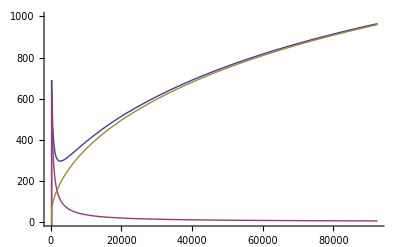

```mathematica
gr1=ListPlot[{datadEdxtotvsE,datadEdxivsE,datadEdxevsE},Joined-> True,PlotRange-> {0,1*10^3}]
```

### interpolating functions for dE/dx

```mathematica
dEdxE=Interpolation[datadEdxtotvsE];
dEdxiE=Interpolation[datadEdxivsE];
dEdxeE=Interpolation[datadEdxevsE];
```

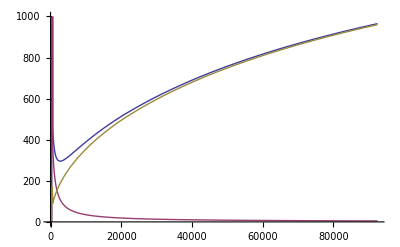

```mathematica
gr2=Plot[{dEdxE[EE],dEdxiE[EE],dEdxeE[EE]},{EE,0,E0},PlotRange-> {0,1*10^3}]
```

```mathematica
(* Show[gr1,gr2] *)
```

### Range: E=E(x)

```mathematica
dxE[e_] :=1/dEdxE[e]
xE[e_]   := NIntegrate[1/dEdxE[Ep],{Ep,e,E0},PrecisionGoal->Automatic]
```

```mathematica
Nmax=100;
emin=1.5*Te;
emax=E0;
dE=(emax-emin)/Nmax;
dataEx=Table[{xE[e],e},{e,emin,emax,dE}] (* Convert dE/dx from MeV/μm to keV/μm *)
dataEx[[1]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Ep near {Ep} = {448.99126362192686`}. NIntegrate obtained 146.517 and 0.0500422 for the integral and error estimates.

{{146.517,1.5},{145.684,926.485},{142.884,1851.47},{139.787,2776.46},{136.68,3701.44},{133.659,4626.43},{130.749,5551.41},{127.955,6476.4},{125.271,7401.38},{122.69,8326.37},{120.203,9251.35},{117.801,10176.3},{115.479,11101.3},{113.228,12026.3},{111.047,12951.3},{108.918,13876.3},{106.85,14801.3},{104.833,15726.2},{102.864,16651.2},{100.941,17576.2},{99.0587,18501.2},{97.216,19426.2},{95.41,20351.2},{93.6386,21276.2},{91.8993,22201.1},{90.1886,23126.1},{88.5067,24051.1},{86.8523,24976.1},{85.2239,25901.1},{83.6202,26826.1},{82.04,27751.1},{80.4823,28676.},{78.9459,29601.},{77.43,30526.},{75.9337,31451.},{74.4561,32376.},{72.9965,33301.},{71.5542,34225.9},{70.1284,35150.9},{68.7186,36075.9},{67.324,37000.9},{65.9443,37925.9},{64.5788,38850.9},{63.2272,39775.9},{61.8894,40700.8},{60.5644,41625.8},{59.2518,42550.8},{57.9513,43475.8},{56.6624,44400.8},{55.3847,45325.8},{54.1179,46250.8},{52.8617,47175.7},{51.6158,48100.7},{50.3799,49025.7},{49.1536,49950.7},{47.9367,50875.7},{46.729,51800.7},{45.5302,52725.6},{44.34,53650.6},{43.1582,54575.6},{41.9846,55500.6},{40.8191,56425.6},{39.6613,57350.6},{38.5111,58275.6},{37.3683,59200.5},{36.2327,60125.5},{35.1041,61050.5},{33.9825,61975.5},{32.8675,62900.5},{31.7591,63825.5},{30.6572,64750.5},{29.5614,65675.4},{28.4719,66600.4},{27.3883,67525.4},{26.3105,68450.4},{25.2385,69375.4},{24.1721,70300.4},{23.1112,71225.3},{22.0556,72150.3},{21.0054,73075.3},{19.9603,74000.3},{18.9202,74925.3},{17.8851,75850.3},{16.8548,76775.3},{15.8293,77700.2},{14.8085,78625.2},{13.7922,79550.2},{12.7804,80475.2},{11.773,81400.2},{10.77,82325.2},{9.77117,83250.2},{8.77652,84175.1},{7.78595,85100.1},{6.7994,86025.1},{5.81678,86950.1},{4.83803,87875.1},{3.86309,88800.1},{2.89187,89725.},{1.92433,90650.},{0.960394,91575.},{0,92500.}}

{146.517,1.5}

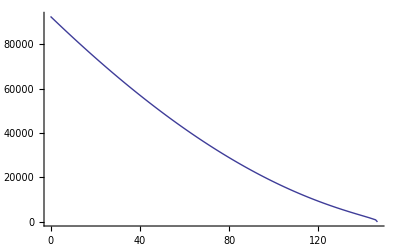

146.517

```mathematica
gr3=ListPlot[dataEx,Joined-> True] (* microns *)
dataEx[[1,1]]
```

### check range consistency with range.f90

```mathematica
nts=99; (* stop reading when Ep goes critical,
            in this case when Ep < 0 *)st=OpenRead["range.003.out"];
Do[Read[st,String],{i,1,19}];
ne=Read[st,Number];
Te=Read[st,Number];
Ti=Read[st,Number];
{Te,Ti,ne}
nn=Read[st,{Number,Number,Number}]
proj=Read[st,{Number,Number,Number}]
data=
Table[Read[st,{Number,Number,Number,Number,Number,Number,Number,Number}],{i,1,nts}];
Close[st];
data;
```

{1.,1.,1.×10^23}

{3.×10^-11,100,10}

{92500.,1.12593×10^8,25.}

```mathematica
scale2=10^4; (* cm to μm *)
Evsx=Table[{data[[i,3]]*scale2,data[[i,5]]},{i,1,nts}];data1=Table[{data[[i,3]],data[[i,6]]},{i,1,nts}];
data2=Table[{data[[i,3]],data[[i,7]]},{i,1,nts}];data3=Table[{data[[i,3]],data[[i,8]]},{i,1,nts}];
data[[44,3]]*10^4
```

105.022

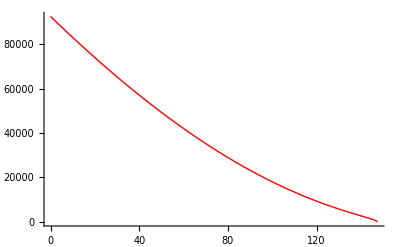

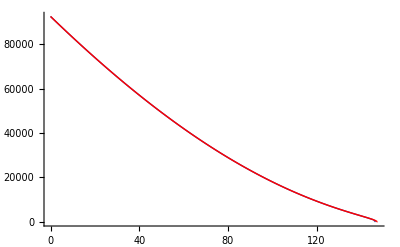

```mathematica
gr4b=ListPlot[Evsx,Joined-> True,PlotStyle-> Red]
Show[gr3,gr4b] (* a simple scaling of E *)
```

## FF: case 3 [range of FF in plasma]: 004

### plotting dE/dx vs E from dedx.out file

```mathematica
st=OpenRead["dedx.004.out"];
Do[Read[st,String],{i,1,19}];
ne=Read[st,Number]
Te=Read[st,Number]
Ti=Read[st,Number]
nn=Read[st,Number]
proj=Read[st,{Number,Number,Number}]
nts=nn+1; (* stop reading when Ep goes critical,
            in this case when Ep < 0 *)
data=
Table[Read[st,{Number,Number,Number,Number,Number}],{i,1,nts}];
Close[st];
data
```

1.×10^23

1.

1.

300

{92500.,1.12593×10^8,25.}

{{0,0.00001,86327.6,86328.,-0.485042},{1,308.333,0.376402,0.298273,0.0781297},{2,616.667,0.268991,0.172186,0.0968054},{3,925.,0.238035,0.123768,0.114267},{4,1233.33,0.227391,0.0975829,0.129808},{5,1541.67,0.224857,0.0810273,0.14383},{6,1850.,0.2262,0.0695345,0.156665},{7,2158.33,0.229631,0.0610745,0.168557},{8,2466.67,0.234233,0.0545573,0.179676},{9,2775.,0.239515,0.0493658,0.190149},{10,3083.33,0.245181,0.0451076,0.200074},{11,3391.67,0.251095,0.0415713,0.209524},{12,3700.,0.257153,0.0385934,0.21856},{13,4008.33,0.263261,0.0360325,0.227229},{14,4316.67,0.26938,0.0338098,0.23557},{15,4625.,0.275488,0.0318709,0.243617},{16,4933.33,0.281546,0.0301493,0.251397},{17,5241.67,0.287543,0.0286094,0.258934},{18,5550.,0.293471,0.0272228,0.266248},{19,5858.33,0.29934,0.0259834,0.273357},{20,6166.67,0.305141,0.0248644,0.280276},{21,6475.,0.310836,0.0238174,0.287019},{22,6783.33,0.316483,0.0228856,0.293598},{23,7091.67,0.322044,0.0220209,0.300023},{24,7400.,0.327517,0.0212125,0.306305},{25,7708.33,0.332935,0.0204846,0.312451},{26,8016.67,0.338255,0.0197858,0.31847},{27,8325.,0.343522,0.0191548,0.324368},{28,8633.33,0.348709,0.0185568,0.330152},{29,8941.67,0.353819,0.0179911,0.335828},{30,9250.,0.358866,0.0174641,0.341401},{31,9558.33,0.363853,0.0169753,0.346877},{32,9866.67,0.368774,0.0165143,0.35226},{33,10175.,0.373625,0.0160716,0.357553},{34,10483.3,0.378408,0.0156469,0.362761},{35,10791.7,0.383156,0.0152683,0.367888},{36,11100.,0.387827,0.0148903,0.372937},{37,11408.3,0.392447,0.0145372,0.37791},{38,11716.7,0.397013,0.0142014,0.382811},{39,12025.,0.401517,0.0138739,0.387643},{40,12333.3,0.405988,0.0135794,0.392409},{41,12641.7,0.410397,0.0132868,0.39711},{42,12950.,0.414756,0.0130072,0.401749},{43,13258.3,0.41906,0.0127323,0.406328},{44,13566.7,0.423335,0.0124864,0.410849},{45,13875.,0.427553,0.0122395,0.415314},{46,14183.3,0.431727,0.0120025,0.419724},{47,14491.7,0.435867,0.0117849,0.424083},{48,14800.,0.439949,0.0115592,0.42839},{49,15108.3,0.444006,0.0113582,0.432648},{50,15416.7,0.448013,0.0111542,0.436858},{51,15725.,0.451979,0.0109576,0.441022},{52,16033.3,0.455918,0.0107779,0.44514},{53,16341.7,0.459818,0.0106039,0.449215},{54,16650.,0.463667,0.010421,0.453246},{55,16958.3,0.467496,0.0102591,0.457236},{56,17266.7,0.471279,0.0100929,0.461186},{57,17575.,0.475037,0.00994143,0.465096},{58,17883.3,0.478753,0.00978576,0.468968},{59,18191.7,0.482446,0.00964371,0.472802},{60,18500.,0.486091,0.00949122,0.476599},{61,18808.3,0.48972,0.00935834,0.480361},{62,19116.7,0.493318,0.00922903,0.484089},{63,19425.,0.496876,0.00909444,0.487781},{64,19733.3,0.500414,0.00897269,0.491441},{65,20041.7,0.503914,0.00884563,0.495069},{66,20350.,0.507395,0.00873081,0.498664},{67,20658.3,0.510847,0.00861885,0.502229},{68,20966.7,0.514259,0.00849614,0.505762},{69,21275.,0.517658,0.00839079,0.509267},{70,21583.3,0.52103,0.00828795,0.512742},{71,21891.7,0.524376,0.00818754,0.516189},{72,22200.,0.526881,0.00808156,0.5188},{73,22508.3,0.53015,0.00798643,0.522163},{74,22816.7,0.533385,0.00788552,0.525499},{75,23125.,0.536604,0.00779528,0.528809},{76,23433.3,0.539798,0.00770703,0.532091},{77,23741.7,0.542969,0.0076207,0.535348},{78,24050.,0.546103,0.00752388,0.53858},{79,24358.3,0.549228,0.00744218,0.541786},{80,24666.7,0.55233,0.0073622,0.544968},{81,24975.,0.55541,0.00728387,0.548126},{82,25283.3,0.55846,0.00719944,0.55126},{83,25591.7,0.561496,0.00712484,0.554371},{84,25900.,0.564511,0.00705173,0.557459},{85,26208.3,0.567498,0.00697266,0.560525},{86,26516.7,0.570471,0.00690293,0.563568},{87,26825.,0.573425,0.00683456,0.56659},{88,27133.3,0.576358,0.00676749,0.569591},{89,27441.7,0.579271,0.00670169,0.57257},{90,27750.,0.582154,0.00662564,0.575528},{91,28058.3,0.58503,0.00656305,0.578467},{92,28366.7,0.587886,0.00650161,0.581385},{93,28675.,0.590724,0.00644129,0.584283},{94,28983.3,0.593543,0.00638204,0.587161},{95,29291.7,0.596338,0.0063167,0.590021},{96,29600.,0.599122,0.00625998,0.592862},{97,29908.3,0.601888,0.00620425,0.595683},{98,30216.7,0.604636,0.00614948,0.598487},{99,30525.,0.607361,0.00608889,0.601273},{100,30833.3,0.610077,0.00603639,0.60404},{101,31141.7,0.612775,0.00598477,0.60679},{102,31450.,0.615457,0.005934,0.609523},{103,31758.3,0.618122,0.00588406,0.612238},{104,32066.7,0.620771,0.00583494,0.614936},{105,32375.,0.623394,0.00577598,0.617618},{106,32683.3,0.626013,0.00572904,0.620284},{107,32991.7,0.628616,0.00568285,0.622933},{108,33300.,0.631203,0.00563737,0.625566},{109,33608.3,0.633775,0.00559261,0.628183},{110,33916.7,0.636333,0.00554853,0.630784},{111,34225.,0.638869,0.00549839,0.633371},{112,34533.3,0.641397,0.005456,0.635941},{113,34841.7,0.643912,0.00541424,0.638497},{114,35150.,0.646411,0.00537311,0.641038},{115,35458.3,0.648897,0.00533258,0.643564},{116,35766.7,0.651362,0.00528629,0.646076},{117,36075.,0.65382,0.00524726,0.648573},{118,36383.3,0.656265,0.0052088,0.651056},{119,36691.7,0.658696,0.00517088,0.653525},{120,37000.,0.661114,0.0051335,0.65598},{121,37308.3,0.663518,0.00509664,0.658422},{122,37616.7,0.66591,0.0050603,0.66085},{123,37925.,0.668289,0.00502446,0.663264},{124,38233.3,0.670645,0.00497931,0.665665},{125,38541.7,0.672998,0.00494492,0.668053},{126,38850.,0.67534,0.004911,0.670429},{127,39158.3,0.677669,0.00487753,0.672791},{128,39466.7,0.679985,0.0048445,0.675141},{129,39775.,0.682639,0.00481191,0.677827},{130,40083.3,0.684937,0.00477974,0.680157},{131,40391.7,0.687224,0.004748,0.682476},{132,40700.,0.689492,0.00471052,0.684782},{133,41008.3,0.691756,0.00467985,0.687076},{134,41316.7,0.694008,0.00464958,0.689358},{135,41625.,0.696249,0.00461969,0.691629},{136,41933.3,0.698478,0.00459017,0.693888},{137,42241.7,0.700697,0.00456102,0.696136},{138,42550.,0.702898,0.00452634,0.698372},{139,42858.3,0.705095,0.00449815,0.700597},{140,43166.7,0.707281,0.00447031,0.702811},{141,43475.,0.709456,0.00444281,0.705013},{142,43783.3,0.711621,0.00441563,0.707205},{143,44091.7,0.713775,0.00438878,0.709386},{144,44400.,0.715919,0.00436225,0.711557},{145,44708.3,0.718053,0.00433603,0.713717},{146,45016.7,0.720176,0.00431011,0.715866},{147,45325.,0.722289,0.0042845,0.718005},{148,45633.3,0.724383,0.00424995,0.720133},{149,45941.7,0.726477,0.00422529,0.722252},{150,46250.,0.728561,0.00420091,0.72436},{151,46558.3,0.730635,0.00417681,0.726458},{152,46866.7,0.732699,0.00415298,0.728546},{153,47175.,0.734754,0.00412941,0.730625},{154,47483.3,0.7368,0.0041061,0.732694},{155,47791.7,0.738836,0.00408305,0.734753},{156,48100.,0.740862,0.00406025,0.736802},{157,48408.3,0.74288,0.0040377,0.738842},{158,48716.7,0.744888,0.00401539,0.740873},{159,49025.,0.746887,0.00399333,0.742894},{160,49333.3,0.748872,0.00396603,0.744906},{161,49641.7,0.750853,0.00394464,0.746909},{162,49950.,0.752826,0.00392347,0.748902},{163,50258.3,0.754789,0.00390252,0.750887},{164,50566.7,0.756744,0.00388179,0.752863},{165,50875.,0.758691,0.00386128,0.754829},{166,51183.3,0.760629,0.00384097,0.756788},{167,51491.7,0.762552,0.00381546,0.758737},{168,51800.,0.764473,0.00379577,0.760678},{169,52108.3,0.766386,0.00377627,0.76261},{170,52416.7,0.76829,0.00375697,0.764533},{171,52725.,0.770186,0.00373785,0.766448},{172,53033.3,0.772074,0.00371893,0.768355},{173,53341.7,0.773954,0.0037002,0.770254},{174,53650.,0.775826,0.00368165,0.772144},{175,53958.3,0.777689,0.00366328,0.774026},{176,54266.7,0.779545,0.00364509,0.7759},{177,54575.,0.781393,0.00362708,0.777766},{178,54883.3,0.783233,0.00360923,0.779624},{179,55191.7,0.785065,0.00359156,0.781474},{180,55500.,0.78689,0.00357406,0.783316},{181,55808.3,0.788699,0.00354843,0.78515},{182,56116.7,0.790508,0.00353153,0.786977},{183,56425.,0.792311,0.00351479,0.788796},{184,56733.3,0.794105,0.00349821,0.790607},{185,57041.7,0.795892,0.00348178,0.792411},{186,57350.,0.797672,0.0034655,0.794207},{187,57658.3,0.799445,0.00344937,0.795996},{188,57966.7,0.80121,0.00343338,0.797777},{189,58275.,0.802968,0.00341754,0.799551},{190,58583.3,0.804719,0.00340184,0.801318},{191,58891.7,0.806463,0.00338629,0.803077},{192,59200.,0.8082,0.00337087,0.804829},{193,59508.3,0.80993,0.00335559,0.806574},{194,59816.7,0.811653,0.00334044,0.808312},{195,60125.,0.813369,0.00332543,0.810043},{196,60433.3,0.815078,0.00331054,0.811767},{197,60741.7,0.816775,0.00329086,0.813484},{198,61050.,0.818471,0.00327639,0.815194},{199,61358.3,0.82016,0.00326204,0.816898},{200,61666.7,0.821842,0.00324782,0.818594},{201,61975.,0.823517,0.00323371,0.820284},{202,62283.3,0.825186,0.00321973,0.821967},{203,62591.7,0.826849,0.00320586,0.823643},{204,62900.,0.828505,0.00319211,0.825313},{205,63208.3,0.830154,0.00317847,0.826976},{206,63516.7,0.831797,0.00316495,0.828632},{207,63825.,0.833429,0.00314672,0.830283},{208,64133.3,0.83506,0.00313356,0.831926},{209,64441.7,0.836684,0.00312051,0.833564},{210,64750.,0.838302,0.00310757,0.835195},{211,65058.3,0.839914,0.00309473,0.836819},{212,65366.7,0.84152,0.00308199,0.838438},{213,65675.,0.843119,0.00306936,0.84005},{214,65983.3,0.844712,0.00305683,0.841656},{215,66291.7,0.8463,0.0030444,0.843255},{216,66600.,0.847881,0.00303207,0.844849},{217,66908.3,0.849456,0.00301983,0.846437},{218,67216.7,0.851026,0.00300769,0.848018},{219,67525.,0.852589,0.00299565,0.849594},{220,67833.3,0.854147,0.0029837,0.851163},{221,68141.7,0.855699,0.00297184,0.852727},{222,68450.,0.857245,0.00296008,0.854285},{223,68758.3,0.858785,0.0029484,0.855837},{224,69066.7,0.860319,0.00293682,0.857383},{225,69375.,0.861848,0.00292532,0.858923},{226,69683.3,0.863364,0.00290648,0.860457},{227,69991.7,0.864882,0.00289535,0.861986},{228,70300.,0.866394,0.00288431,0.863509},{229,70608.3,0.8679,0.00287335,0.865027},{230,70916.7,0.869401,0.00286248,0.866539},{231,71225.,0.870897,0.00285168,0.868045},{232,71533.3,0.872387,0.00284097,0.869546},{233,71841.7,0.873872,0.00283033,0.871041},{234,72150.,0.875351,0.00281977,0.872531},{235,72458.3,0.876825,0.00280929,0.874016},{236,72766.7,0.878293,0.00279889,0.875495},{237,73075.,0.879757,0.00278856,0.876968},{238,73383.3,0.881214,0.0027783,0.878436},{239,73691.7,0.882667,0.00276812,0.879899},{240,74000.,0.884115,0.00275801,0.881357},{241,74308.3,0.885557,0.00274798,0.882809},{242,74616.7,0.886994,0.00273801,0.884256},{243,74925.,0.888426,0.00272812,0.885698},{244,75233.3,0.889853,0.00271829,0.887135},{245,75541.7,0.891275,0.00270854,0.888566},{246,75850.,0.892692,0.00269885,0.889993},{247,76158.3,0.894103,0.00268923,0.891414},{248,76466.7,0.895506,0.00267523,0.89283},{249,76775.,0.896907,0.00266585,0.894242},{250,77083.3,0.898304,0.00265653,0.895648},{251,77391.7,0.899696,0.00264728,0.897049},{252,77700.,0.901084,0.0026381,0.898445},{253,78008.3,0.902466,0.00262897,0.899837},{254,78316.7,0.903843,0.00261991,0.901223},{255,78625.,0.905216,0.0026109,0.902605},{256,78933.3,0.906584,0.00260196,0.903982},{257,79241.7,0.907947,0.00259308,0.905354},{258,79550.,0.909305,0.00258426,0.906721},{259,79858.3,0.910659,0.00257549,0.908083},{260,80166.7,0.912008,0.00256679,0.909441},{261,80475.,0.913352,0.00255814,0.910794},{262,80783.3,0.914687,0.00254519,0.912142},{263,81091.7,0.916022,0.00253675,0.913485},{264,81400.,0.917353,0.00252837,0.914824},{265,81708.3,0.918679,0.00252004,0.916159},{266,82016.7,0.92,0.00251177,0.917488},{267,82325.,0.921317,0.00250355,0.918813},{268,82633.3,0.922629,0.00249538,0.920134},{269,82941.7,0.923937,0.00248727,0.92145},{270,83250.,0.92524,0.00247921,0.922761},{271,83558.3,0.926539,0.0024712,0.924068},{272,83866.7,0.927834,0.00246323,0.92537},{273,84175.,0.929124,0.00245532,0.926668},{274,84483.3,0.930409,0.00244746,0.927962},{275,84791.7,0.931691,0.00243965,0.929251},{276,85100.,0.932968,0.00243189,0.930536},{277,85408.3,0.93424,0.00242417,0.931816},{278,85716.7,0.935509,0.00241651,0.933092},{279,86025.,0.936773,0.00240889,0.934364},{280,86333.3,0.938033,0.00240131,0.935631},{281,86641.7,0.939288,0.00239379,0.936894},{282,86950.,0.940539,0.00238631,0.938153},{283,87258.3,0.941787,0.00237887,0.939408},{284,87566.7,0.943029,0.00237148,0.940658},{285,87875.,0.944268,0.00236414,0.941904},{286,88183.3,0.945503,0.00235684,0.943146},{287,88491.7,0.946733,0.00234958,0.944384},{288,88800.,0.94796,0.00234237,0.945617},{289,89108.3,0.949182,0.0023352,0.946847},{290,89416.7,0.950393,0.00232147,0.948072},{291,89725.,0.951607,0.00231452,0.949293},{292,90033.3,0.952818,0.00230761,0.95051},{293,90341.7,0.954024,0.00230075,0.951723},{294,90650.,0.955226,0.00229392,0.952932},{295,90958.3,0.956424,0.00228714,0.954137},{296,91266.7,0.957618,0.00228039,0.955338},{297,91575.,0.958808,0.00227368,0.956535},{298,91883.3,0.959994,0.00226701,0.957727},{299,92191.7,0.961177,0.00226038,0.958916},{300,92500.,0.962355,0.00225379,0.960101}}

```mathematica
datadEdxtotvsE=Table[{data[[i,2]],data[[i,3]]*10^3},{i,1,nts}];
datadEdxivsE=Table[{data[[i,2]],data[[i,4]]*10^3},{i,1,nts}];datadEdxevsE=Table[{data[[i,2]],data[[i,5]]*10^3},{i,1,nts}];
E0=datadEdxtotvsE[[nts,1]]
(* convert from MeV/μm to keV/μm *)
```

92500.

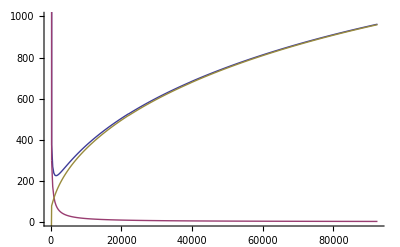

```mathematica
gr1=ListPlot[{datadEdxtotvsE,datadEdxivsE,datadEdxevsE},Joined-> True,PlotRange-> {0,1*10^3}]
```

### interpolating functions for dE/dx

```mathematica
dEdxE=Interpolation[datadEdxtotvsE];
dEdxiE=Interpolation[datadEdxivsE];
dEdxeE=Interpolation[datadEdxevsE];
```

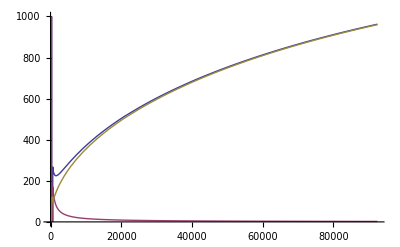

```mathematica
gr2=Plot[{dEdxE[EE],dEdxiE[EE],dEdxeE[EE]},{EE,0,E0},PlotRange-> {0,1*10^3}]
```

```mathematica
(* Show[gr1,gr2] *)
```

### Range: E=E(x)

```mathematica
dxE[e_] :=1/dEdxE[e]
xE[e_]   := NIntegrate[1/dEdxE[Ep],{Ep,e,E0},PrecisionGoal->Automatic]
```

```mathematica
Nmax=100;
emin=1.5*Te;
emax=E0;
dE=(emax-emin)/Nmax;
dataEx=Table[{xE[e],e},{e,emin,emax,dE}] (* Convert dE/dx from MeV/μm to keV/μm *)
dataEx[[1]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Ep near {Ep} = {451.8136252244966`}. NIntegrate obtained 152.84 and 0.0433618 for the integral and error estimates.

{{152.84,1.5},{151.562,926.485},{147.494,1851.47},{143.509,2776.46},{139.781,3701.44},{136.307,4626.43},{133.055,5551.41},{129.994,6476.4},{127.096,7401.38},{124.339,8326.37},{121.706,9251.35},{119.18,10176.3},{116.751,11101.3},{114.407,12026.3},{112.141,12951.3},{109.945,13876.3},{107.813,14801.3},{105.738,15726.2},{103.718,16651.2},{101.748,17576.2},{99.8228,18501.2},{97.9409,19426.2},{96.0989,20351.2},{94.2942,21276.2},{92.524,22201.1},{90.7845,23126.1},{89.0759,24051.1},{87.3965,24976.1},{85.7446,25901.1},{84.119,26826.1},{82.5181,27751.1},{80.9409,28676.},{79.3861,29601.},{77.8528,30526.},{76.3399,31451.},{74.8467,32376.},{73.3722,33301.},{71.9156,34225.9},{70.4763,35150.9},{69.0535,36075.9},{67.6466,37000.9},{66.2551,37925.9},{64.8782,38850.9},{63.5157,39775.9},{62.1675,40700.8},{60.8325,41625.8},{59.5103,42550.8},{58.2005,43475.8},{56.9026,44400.8},{55.6163,45325.8},{54.3412,46250.8},{53.077,47175.7},{51.8234,48100.7},{50.5799,49025.7},{49.3464,49950.7},{48.1225,50875.7},{46.9079,51800.7},{45.7025,52725.6},{44.5058,53650.6},{43.3179,54575.6},{42.1383,55500.6},{40.9668,56425.6},{39.8033,57350.6},{38.6475,58275.6},{37.4993,59200.5},{36.3585,60125.5},{35.2248,61050.5},{34.0982,61975.5},{32.9784,62900.5},{31.8652,63825.5},{30.7586,64750.5},{29.6584,65675.4},{28.5644,66600.4},{27.4765,67525.4},{26.3945,68450.4},{25.3184,69375.4},{24.248,70300.4},{23.1831,71225.3},{22.1237,72150.3},{21.0697,73075.3},{20.0209,74000.3},{18.9772,74925.3},{17.9385,75850.3},{16.9048,76775.3},{15.8759,77700.2},{14.8517,78625.2},{13.8322,79550.2},{12.8172,80475.2},{11.8067,81400.2},{10.8005,82325.2},{9.79869,83250.2},{8.80106,84175.1},{7.80757,85100.1},{6.81815,86025.1},{5.83271,86950.1},{4.8512,87875.1},{3.87353,88800.1},{2.89965,89725.},{1.92947,90650.},{0.962941,91575.},{0,92500.}}

{152.84,1.5}

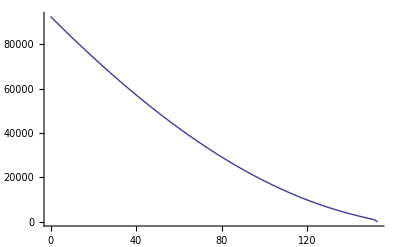

152.84

```mathematica
gr3=ListPlot[dataEx,Joined-> True] (* microns *)
dataEx[[1,1]]
```

### check range consistency with range.f90

```mathematica
nts=99; (* stop reading when Ep goes critical,
            in this case when Ep < 0 *)st=OpenRead["range.004.out"];
Do[Read[st,String],{i,1,19}];
ne=Read[st,Number];
Te=Read[st,Number];
Ti=Read[st,Number];
{Te,Ti,ne}
nn=Read[st,{Number,Number,Number}]
proj=Read[st,{Number,Number,Number}]
data=
Table[Read[st,{Number,Number,Number,Number,Number,Number,Number,Number}],{i,1,nts}];
Close[st];
data;
```

{1.,1.,1.×10^23}

{3.×10^-11,100,10}

{92500.,1.12593×10^8,25.}

```mathematica
scale2=10^4; (* cm to μm *)
Evsx=Table[{data[[i,3]]*scale2,data[[i,5]]},{i,1,nts}];data1=Table[{data[[i,3]],data[[i,6]]},{i,1,nts}];
data2=Table[{data[[i,3]],data[[i,7]]},{i,1,nts}];data3=Table[{data[[i,3]],data[[i,8]]},{i,1,nts}];
data[[nts,3]]*10^4
```

152.102

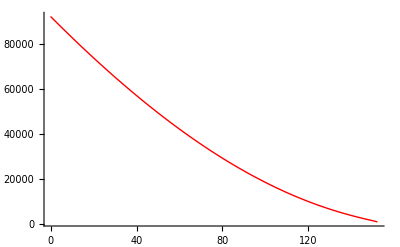

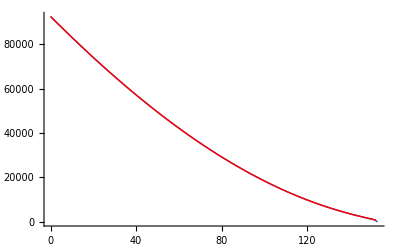

```mathematica
gr4b=ListPlot[Evsx,Joined-> True,PlotStyle-> Red]
Show[gr3,gr4b] (* a simple scaling of E *)
```